# Diamond Robot

## Modellation and Control

## Package Loading

```mathematica
PrependTo[$Path,NotebookDirectory[]];
```

```mathematica
<<ScrewCalculusPro`
```

```mathematica
?ScrewCalculusPro`*
```

## Double parallelogram linkage

## Parameters

### Configuration

```mathematica
qAlist = {q1,q2};
qNAlist= {off1,qn2, qn3, off4, qn5, qn6};
```

```mathematica
qA[t_] = #[t]&/@qAlist;
qNA[t_]=#[t]&/@qNAlist;
```

### Parameters

```mathematica
alistB= {a1,b1};
alistP = {a2,a1,a2,b2,b1,b2};
masslistB = {m1,m2};
masslistP={m3,m4,m5,m6,m7,m8};
rlistB = {r1,r2};
rlistP = {r3,r4,r5,r6,r7,r8};
V[r_,a_]= Pi*r^2*a;
```

```mathematica
Integrand =(#.#ᵀ)&@ Hat[{x,y,z}];
changevar = {x,y,z}->{r Cos[θ], r Sin[θ], z}//Thread;
IntegrandCC = Integrand/.changevar;
J[R_, L_, m_]= Integrate[IntegrandCC *r* m / V[R,L], {r,0,R},{θ,0,2Pi},{z,-L/2,L/2}]//FullSimplify;
```

```mathematica
JlistB = J@@#&/@Transpose[{rlistB, alistB, masslistB}];
JlistP = J@@#&/@Transpose[{rlistP, alistP, masslistP}];
```

```mathematica
CGlistB= {{-a1+la1,0,0},{-b1+lb1,0,0}};
CGlistP = {{-a2+lP1,0,0},{-a1+lP2,0,0},{-a2+lP3,0,0},{-b2+lP4,0,0},{-b1+lP5,0,0},{-b2+lP6,0,0}};
```

```mathematica
g0 = {0,-g,0};
```

### DH

```mathematica
DHB= {#1,0,0,#2,"R"}&@@#&/@Transpose[{alistB, qAlist}];
DHP =  {#1,0,0,#2,"R"}&@@#&/@Transpose[{alistP, qNAlist}];
```

### Reference

```mathematica
Tb0 = HomogeneousTranslX[d1];
Ten = IdentityMatrix[4];
ref = {Tb0, Ten};
```

## Chain Closure

```mathematica
TB = DHFKine[DHB,ref]//FullSimplify;
TP = DHFKine[DHP,ref]//FullSimplify;
```

```mathematica
p1B = RigidPosition[DHFKine[DHB,ref,1]]//FullSimplify;
p1P =  RigidPosition[DHFKine[DHP,ref,3]]//FullSimplify;
```

```mathematica
p2B = RigidPosition[DHFKine[DHB,ref]]//FullSimplify;
p2P =  RigidPosition[DHFKine[DHP,ref]]//FullSimplify;
```

```mathematica
eqclp1 = FullSimplify[p1B-p1P]=={0,0,0}//Thread;
eqclp2 = FullSimplify[p2B-p2P] == {0,0,0}//Thread;
eqnsclosure = Join[eqclp1, eqclp2];
```

```mathematica
eqclp1//MatrixForm
```

(a1 Cos[q1]-a1 Cos[off1+qn2]-a2 (Cos[off1]+Cos[off1+qn2+qn3])==0
a1 Sin[q1]-a1 Sin[off1+qn2]-a2 (Sin[off1]+Sin[off1+qn2+qn3])==0
True)

```mathematica
RigidOrientation[DHFKine[DHP12[q1,q2],ref]]//FullSimplify //MatrixForm // TeXForm
```

\text{RigidOrientation}\left(\left(
\begin{array}{cccc}
 1 & 0 & 0 & \text{d1} \\
 0 & 1 & 0 & 0 \\
 0 & 0 & 1 & 0 \\
 0 & 0 & 0 & 1 \\
\end{array}
\right).\text{DH}(\text{q1}).\text{DH}(\text{q2}).\left(
\begin{array}{cccc}
 1 & 0 & 0 & 0 \\
 0 & 1 & 0 & 0 \\
 0 & 0 & 1 & 0 \\
 0 & 0 & 0 & 1 \\
\end{array}
\right)\right)

```mathematica
neweqp1 = {q1 == off1 + qn2, off1 == off1+qn2+qn3+Pi}//FullSimplify;
```

```mathematica
solp1 = Solve[neweqp1, {qn2, qn3},Reals]//First;
```

```mathematica
eqclp1/.solp1//MatrixForm
```

(True
True
True)

```mathematica
qn23[q1_]= {qn2,qn3}/.solp1
```

{-off1+q1,off1-π-q1}

```mathematica
eqclp2/.solp1//FullSimplify//MatrixForm
```

(b1 (Cos[q1+q2]+Cos[off1+off4+qn5])+b2 (Cos[off1+off4]+Cos[off1+off4+qn5+qn6])==0
b1 (Sin[q1+q2]+Sin[off1+off4+qn5])+b2 (Sin[off1+off4]+Sin[off1+off4+qn5+qn6])==0
True)

```mathematica
neweqp2 = {q1+q2 == off1+off4+qn5+Pi, off1+off4 == off1+off4+qn5+qn6 + Pi}//FullSimplify;
```

```mathematica
solp2 = Solve[neweqp2,{qn5,qn6},Reals]//First;
```

```mathematica
eqclp2/.solp1/.solp2//MatrixForm
```

(True
True
True)

```mathematica
qn56[q1_,q2_]={qn5,qn6}/.solp2;
```

```mathematica
qnaf[q1_,q2_]=qNAlist/.solp1/.solp2//FullSimplify//Flatten;
```

```mathematica
S1 = D[qnaf[q1,q2],{{q1,q2}}];
```

```mathematica
S = Join[IdentityMatrix[2],S1];
```

```mathematica
qnadot = S.{q1'[t],q2'[t]};
```

```mathematica
DHP12[q1_,q2_]= DHP/.solp1 /.solp2;
```

```mathematica
TP12[q1_,q2_]=DHFKine[DHP12[q1,q2],ref]//FullSimplify;
```

```mathematica
p2B//MatrixForm
```

(d1+a1 Cos[q1]+b1 Cos[q1+q2]
a1 Sin[q1]+b1 Sin[q1+q2]
0)

```mathematica
p2P/.solp1/.solp2//MatrixForm
```

(d1+a1 Cos[q1]+b1 Cos[q1+q2]
a1 Sin[q1]+b1 Sin[q1+q2]
0)

```mathematica
TP12[q1,q2]//MatrixForm//TeXForm
```

\left(
\begin{array}{cccc}
 \cos (\text{off1}+\text{off4}) & -\sin (\text{off1}+\text{off4}) & 0 & \text{a1} \cos (\text{q1})+\text{b1} \cos
   (\text{q1}+\text{q2})+\text{d1} \\
 \sin (\text{off1}+\text{off4}) & \cos (\text{off1}+\text{off4}) & 0 & \text{a1} \sin (\text{q1})+\text{b1} \sin
   (\text{q1}+\text{q2}) \\
 0 & 0 & 1 & 0 \\
 0 & 0 & 0 & 1 \\
\end{array}
\right)

```mathematica
RigidPosition@TP12[q1,q2]//MatrixForm//TeXForm
```

\left(
\begin{array}{c}
 \text{a1} \cos (\text{q1})+\text{b1} \cos (\text{q1}+\text{q2})+\text{d1} \\
 \text{a1} \sin (\text{q1})+\text{b1} \sin (\text{q1}+\text{q2}) \\
 0 \\
\end{array}
\right)

## Jacobians

```mathematica
JB = DHJacobBase[DHB,Tb0]//FullSimplify;
```

```mathematica
JP[q1_,q2_] = DHJacobBase[DHP12[q1, q2], Tb0].S1//FullSimplify;
```

```mathematica
JP[q1,q2]//MatrixForm
```

(-a1 Sin[q1]-b1 Sin[q1+q2] | -b1 Sin[q1+q2]
a1 Cos[q1]+b1 Cos[q1+q2] | b1 Cos[q1+q2]
0 | 0
0 | 0
0 | 0
0 | 0)

## Dynamics

```mathematica
BB = InertiaBase[DHB, CGlistB, masslistB, JlistB, ref]//FullSimplify;
```

```mathematica
GB = GravitationalBase[DHB, CGlistB, masslistB, g0,ref]//FullSimplify;
```

```mathematica
BP = InertiaBase[DHP12[q1,q2], CGlistP, masslistP, JlistP, ref]//Simplify;
```

```mathematica
GP = GravitationalBase[DHP12[q1,q2], CGlistP, masslistP,g0, ref]//FullSimplify;
```

```mathematica
Btot= ArrayFlatten[{
{BB,0},
{0,BP}
}];
```

```mathematica
Gtot= Join[GB, GP];
```

```mathematica
Ba = Sᵀ.Btot.S//FullSimplify;
```

```mathematica
Ca = InertiaToCoriolis[Ba, qAlist, qA'[t]]//FullSimplify;
```

```mathematica
Ga = Sᵀ.Gtot//FullSimplify;
```

## The other leg

## Parameters

### Configuration

```mathematica
qLlist = {ql1, ql2};
qL[t_]=#[t]&/@qLlist;
```

### Parameters

```mathematica
alistL= {al1, al2};
masslistL = {ml1,ml2};
rlistL = {rl1,rl2};
```

```mathematica
JlistL = J@@#&/@(Transpose[{rlistL, alistL, masslistL}]);
```

```mathematica
CGlistL= {{-al1+ll1,0,0},{-al2+ll2,0,0}};
```

### DH

```mathematica
DHL= {#1,0,0,#2,"R"}&@@#&/@Transpose[{alistL, qLlist}];
```

### Reference

```mathematica
Tb0l = HomogeneousTranslX[-d1];
Tenl = HomogeneousRotZ[ql3];
refl = {Tb0l, Tenl};
```

## Kinematics

```mathematica
TL = DHFKine[DHL,refl]//FullSimplify;
```

```mathematica
JL = DHJacobBase[DHL, Tb0l]//FullSimplify;
```

```mathematica
TL//MatrixForm//TeXForm
```

\left(
\begin{array}{cccc}
 \cos (\text{ql1}+\text{ql2}+\text{ql3}) & -\sin (\text{ql1}+\text{ql2}+\text{ql3}) & 0 & \text{al1} \cos
   (\text{ql1})+\text{al2} \cos (\text{ql1}+\text{ql2})-\text{d1} \\
 \sin (\text{ql1}+\text{ql2}+\text{ql3}) & \cos (\text{ql1}+\text{ql2}+\text{ql3}) & 0 & \text{al1} \sin
   (\text{ql1})+\text{al2} \sin (\text{ql1}+\text{ql2}) \\
 0 & 0 & 1 & 0 \\
 0 & 0 & 0 & 1 \\
\end{array}
\right)

## Dynamics

```mathematica
BL = InertiaBase[DHL, CGlistL, masslistL, JlistL, refl]//FullSimplify;
```

```mathematica
CL = InertiaToCoriolis[BL, qLlist, qL'[t]]//FullSimplify;
```

```mathematica
GL = GravitationalBase[DHL, CGlistL,masslistL,g0,refl]//FullSimplify;
```

```mathematica
BL//MatrixForm
```

(ll1^2 ml1+1/2 (ml1 rl1^2+ml2 (2 (al1^2+ll2^2)+rl2^2))+2 al1 ll2 ml2 Cos[ql2] | 1/2 ml2 (2 ll2^2+rl2^2+2 al1 ll2 Cos[ql2])
1/2 ml2 (2 ll2^2+rl2^2+2 al1 ll2 Cos[ql2]) | 1/2 ml2 (2 ll2^2+rl2^2))

## Chain Close

## Parameters

### configuration

```mathematica
qdAlist = {q1,ql1};
```

```mathematica
qdNAlist = {q2,ql2};
```

```mathematica
qdA[t_]=#[t]&/@qdAlist;
qdNA[t_]=#[t]&/@qdNAlist;
```

```mathematica
qtotlist = {q1,q2,ql1,ql2};
```

```mathematica
qtot[t_]=#[t]&/@qtotlist;
```

```mathematica
Sa = {{1,0},{0,0},{0,1},{0,0}}ᵀ;
```

```mathematica
Sna = {{0,0},{1,0},{0,0},{0,1}}ᵀ;
```

```mathematica
Stot = Join[Sa,Sna];
```

## Coupler

### Configuration

```mathematica
qEElist = {xEE, yEE,γ};
```

```mathematica
qEE[t_]=#[t]&/@qEElist;
```

## Numerical values

```mathematica
n1 = 0.3;
n2 = 0.8;
r = 0.03;
m = 1;
rlist = Join[rlistB,rlistP,rlistL];
rlistnum = {3/2r,r,r/5, r/5,r/5,r/5, r/5,r/5,3/2r,r};
mlist = Join[masslistB,masslistP, masslistL,{me}];
mlistnum = {m,m/8, m/12, m/12, m/12, m/12, m/12, m/12,m,m/8,1};
paramslist = Join[{a1,b1, a2, b2, d1, f, al1, al2, off1,off4,q3, fy, fz,g},rlist,mlist];
numlist =Join[{n1,n2,n1/2, n1/3,0.3,0.2, n1, n2, Pi/3, -2Pi/3,0,0.05,0.05, 9.8},rlistnum,mlistnum]; 
numlaw1 = paramslist->numlist//Thread;
llist = {la1,lb1,lP1,lP2,lP3,lP4,lP5,lP6,ll1,ll2};
llistnum = {a1/2, b1/2, a2/2, a1/2,a2/2, b2/2, b1/2, b2/2, al1/2, al2/2}/.numlaw1;
numlaw = Join[numlaw1,Thread[llist->llistnum]];
```

## Kinematics

### Chain closure

```mathematica
TR[q1_,q2_,q3_]=TP12[q1,q2].HomogeneousRotZ[q3]//FullSimplify;
```

```mathematica
TE = RPToHomogeneous[RotZ[γ],{xEE,yEE,0}];
```

```mathematica
TER = HomogeneousTranslX[f].HomogeneousRotZ@Pi;
```

```mathematica
TEL = HomogeneousTranslX[-f];
```

Position Constraints

```mathematica
eqpR = RigidPosition[TE.TER-TR[q1,q2,q3]]=={0,0,0}//FullSimplify//Thread;
```

```mathematica
eqpL = RigidPosition[TE.TEL-TL]=={0,0,0}//FullSimplify//Thread;
```

Orientation Constraints

```mathematica
RER = RigidOrientation[TE.TER];
```

```mathematica
RR = RigidOrientation[TR[q1,q2,q3]];
```

```mathematica
eqoR = MapThread[Equal,{RER.RRᵀ,IdentityMatrix@3},2]//Flatten//FullSimplify;
```

```mathematica
eqoR//MatrixForm
```

(1+Cos[off1+off4+q3-γ]==0
Sin[off1+off4+q3-γ]==0
True
Sin[off1+off4+q3-γ]==0
1+Cos[off1+off4+q3-γ]==0
True
True
True
True)

```mathematica
eqoRindip = {off1+off4+q3-γ == Pi};
```

```mathematica
eqclR = Join[eqoRindip,eqpR]//FullSimplify;
```

```mathematica
eqclTOT = Join[eqclR, eqpL]//FullSimplify;
```

```mathematica
solq3 = Solve[eqclTOT[[1]],q3,Reals]//First;
```

```mathematica
eqclTOT2 = eqclTOT[[2;;Length@eqclTOT]]/.solq3//FullSimplify;
```

```mathematica
eqclTOT2//MatrixForm
```

(d1+a1 Cos[q1]+b1 Cos[q1+q2]==xEE+f Cos[γ]
yEE+f Sin[γ]==a1 Sin[q1]+b1 Sin[q1+q2]
True
d1+xEE==al1 Cos[ql1]+al2 Cos[ql1+ql2]+f Cos[γ]
yEE==al1 Sin[ql1]+al2 Sin[ql1+ql2]+f Sin[γ]
True)

### Inverse kinematic

Left

```mathematica
eqL = eqpL[[1;;2]];
```

```mathematica
eqtemp = {d1+xEE-f Cos[γ] == al1 Cos[ql1] + al2 Cos[ql1+ql2],yEE - f Sin[γ] == al1 Sin[ql1] + al2 Sin[ql1+ql2]};
```

```mathematica
neweqtemp =( eqtemp[[1,1]]^2+eqtemp[[2,1]]^2 == eqtemp[[1,2]]^2+eqtemp[[2,2]]^2 //FullSimplify)/.Cos[ql2]->Cql2;
```

```mathematica
sol = Solve[neweqtemp, Cql2,Reals]//First;
```

```mathematica
Cql2sol = Cql2/.sol;
```

```mathematica
Sql2sol = Sqrt[1-Cql2sol^2];
```

```mathematica
ql2sol = ArcCos[Cql2sol];
```

```mathematica
ql1sol = ArcTan[xEE+d1-f Cos[γ],yEE-f Sin[γ]] - ArcTan[al1 + al2 Cql2sol,al2 Sql2sol];
qLsol[xEE_,yEE_,γ_]={ql1sol, ql2sol};
```

Right

```mathematica
eqR = eqclR[[2;;3]];
```

```mathematica
eqtemp = {xEE + f Cos[γ] - d1 == a1 Cos[q1] + b1 Cos[q1+q2],eqR[[2]]};
```

```mathematica
eqvar2=( eqtemp[[1,1]]^2+eqtemp[[2,1]]^2 == eqtemp[[1,2]]^2+eqtemp[[2,2]]^2 //FullSimplify)/.Cos[q2]->Cq2;
```

```mathematica
solC2 =Solve[eqvar2, Cq2, Reals]//First//FullSimplify;
```

```mathematica
C2sol = Cq2/.solC2//FullSimplify;
```

```mathematica
S2sol = Sqrt[1-C2sol^2]//FullSimplify;
```

```mathematica
solq1 = ArcTan[xEE-d1+f Cos[γ],yEE+f Sin[γ]] + ArcTan[a1 + b1*C2sol,b1*S2sol];
```

```mathematica
q2sol =- ArcCos[C2sol];
```

```mathematica
q1sol = solq1;
```

```mathematica
qRsol[xEE_, yEE_, γ_] ={q1sol, q2sol};
```

```mathematica
qSol[xEE_,yEE_,γ_]=Join[qRsol[xEE,yEE,γ],qLsol[xEE,yEE,γ]];
```

```mathematica
ArcTan[xEE-d1+f Cos[γ],yEE+f Sin[γ]] + ArcTan[a1 + b1*C2sol,b1*S2sol]//Hold//MatrixForm//TeXForm
```

\text{Hold}\left[\tan ^{-1}(\text{a1}+\text{b1} \text{C2sol},\text{b1} \text{S2sol})+\tan ^{-1}(-\text{d1}+f \cos
   (\gamma )+\text{xEE},f \sin (\gamma )+\text{yEE})\right]

## GRAPHIC TEST

```mathematica
DrawParallelogram[q1_, q2_]:= Module[{plist1,plist, cyllist, gtot},
plist1= RigidPosition[DHFKine[DHP12[q1,q2], ref, #]]&/@Range@6;
plist = Prepend[plist1,RigidPosition[Tb0]];
cyllist = {Orange, Opacity[.7],Cylinder[{plist[[#]],plist[[#+1]]},1.6*rlistP[[#]]]}&/@Range[Length@plist1 ];
gtot = Graphics3D[cyllist/.numlaw//Flatten]
];
```

```mathematica
DrawParallelogram[0,0];
```

```mathematica
DrawArmR[t1_, t2_]:= Block[{qtemp,plist1,plist, cyllist, gtot,DHb},
DHb = DHB/.Thread[{q1,q2}->{t1,t2}];
plist1= RigidPosition[DHFKine[DHb, ref, #]]&/@Range@2;
plist = Prepend[plist1,RigidPosition[Tb0]];
cyllist = {Gray, Opacity[.8],Cylinder[{plist[[#]],plist[[#+1]]},rlist[[#]]]}&/@Range[Length@plist1 ];
gtot = Graphics3D[cyllist/.numlaw//Flatten]
];
```

```mathematica
DrawArmR[0,-Pi/2-Pi/7];
```

```mathematica
DrawArmL[t1_, t2_]:= Block[{qtemp,plist1,plist, cyllist, gtot,DHl},
DHl = DHL/.Thread[{ql1,ql2}->{t1,t2}];
plist1= RigidPosition[DHFKine[DHl, refl, #]]&/@Range@2;
plist = Prepend[plist1,RigidPosition[Tb0l]];
cyllist = {Gray, Opacity[.8],Cylinder[{plist[[#]],plist[[#+1]]},rlistL[[#]]]}&/@Range[Length@plist1 ];
gtot = Graphics3D[cyllist/.numlaw//Flatten]
];
```

```mathematica
DrawCoupler[x_,y_,γ_]:= Module[{center,pmin,pmax},
center = {x,y,0};
pmin = center + RotZ[γ].{-f,-fy,-fz};
pmax = center + RotZ[γ].{f,fy,fz};
Graphics3D@{Red,Opacity[.5],Cuboid[pmin,pmax]/.numlaw}
];
```

```mathematica
Show[DrawCoupler[0,0,0], Boxed-> False]
```

-Graphics3D-

```mathematica
DrawSupport =Module[{latox,latoy,latoz,origin,Ci,Di,Ei,A,B,F,R,a,off},
off = -0.25;
latox = d1*2 + 0.5;
latoy = 0.3;
latoz = 0.5;
origin = -{latox/2,latoy/2,latoz+r};
a = 1.4;
R = 0.05;
A = {-latox - 0.1,-a,off};
B = A + {0,a - R,0};
Ci = {+latox + 0.1,-a,off};
Di = Ci + {0,a- R,0};
Ei = {-latox/2,0,off};
F = {latox/2,0,off};
Graphics3D[{Brown,Opacity[.7], Parallelepiped[origin,IdentityMatrix[3]*{latox,latoy,latoz}], Black, Opacity[.7],Cylinder[{A,B},R],Black, Opacity[.7],Cylinder[{Ci,Di},R],Black, Opacity[.7],Cylinder[{B+{-R,R,0},Ei},R],Black, Opacity[.7],Cylinder[{Di+{R,R,0},F},R]}/.numlaw]
];
```

```mathematica
DrawBackground =Module[{p,v,a},
a = 1.4;
p = {-a,-a,-a};
v = IdentityMatrix[3]*{2a,-0.1,2a};
 Graphics3D[{Green, Opacity[0.9],Parallelepiped[p,v]}]
];
```

```mathematica
DrawFreeScene[q1_,q2_,ql1_,ql2_,x_,y_,γ_]:= Module[{a = 1.5},
Show[DrawParallelogram[q1,q2], DrawArmR[q1,q2],DrawArmL[ql1,ql2],DrawSupport, DrawCoupler[x,y,γ], DrawBackground, Boxed->False, ViewPoint-> Top, PlotRange-> a*{{-1,1},{-1,0.3},{-1,1}}]
];
```

```mathematica
DrawFreeScene[-Pi/4,-Pi/2,-Pi/4,-Pi/2,0,-0.6,0]
```

-Graphics3D-

```mathematica
DrawSceneKinInv[x_,y_,γ_]:= Module[{input},
input = Join[qRsol[x,y, γ],qLsol[x,y, γ],{x,y,γ}]/.numlaw;
DrawFreeScene@@input
];
```

```mathematica
DrawSceneKinInv[0,-0.7,0]
```

-Graphics3D-

## Singularity analisis

```mathematica
eqclTOT//MatrixForm
```

(off1+off4+q3==π+γ
d1+a1 Cos[q1]+b1 Cos[q1+q2]==xEE+f Cos[γ]
yEE+f Sin[γ]==a1 Sin[q1]+b1 Sin[q1+q2]
True
d1+xEE==al1 Cos[ql1]+al2 Cos[ql1+ql2]+f Cos[γ]
yEE==al1 Sin[ql1]+al2 Sin[ql1+ql2]+f Sin[γ]
True)

```mathematica
eqclTOTdk = {d1+a1 Cos[q1] + b1 Cos[q1+q2] -f Cos[γ] == al1 Cos[ql1] + al2 Cos[ql1+ql2] + f Cos[γ] - d1,
a1 Sin[q1] + b1 Sin[q1+q2] - f Sin[γ] == al1 Sin[ql1] + al2 Sin[ql1+ql2] + f Sin[γ]}//FullSimplify
```

{2 d1+a1 Cos[q1]+b1 Cos[q1+q2]==al1 Cos[ql1]+al2 Cos[ql1+ql2]+2 f Cos[γ],a1 Sin[q1]+b1 Sin[q1+q2]==al1 Sin[ql1]+al2 Sin[ql1+ql2]+2 f Sin[γ]}

```mathematica
eqclTOTdkconstr = eqclTOTdk[[All,1]]-eqclTOTdk[[All,2]]=={0,0};
```

```mathematica
V = eqclTOTdkconstr[[1]]
```

{2 d1+a1 Cos[q1]+b1 Cos[q1+q2]-al1 Cos[ql1]-al2 Cos[ql1+ql2]-2 f Cos[γ],a1 Sin[q1]+b1 Sin[q1+q2]-al1 Sin[ql1]-al2 Sin[ql1+ql2]-2 f Sin[γ]}

```mathematica
JV = D[V, {{q2,ql2}}];
```

```mathematica
JVdet = Det[JV]//FullSimplify
```

al2 b1 Sin[q1+q2-ql1-ql2]

## Differential Kinematic

```mathematica
FL = Join[ZeroMatrix[3,3],IdentityMatrix[3]];
```

```mathematica
HL = Join[IdentityMatrix[3],ZeroMatrix[3,3]]ᵀ;
```

```mathematica
FR = ZeroMatrix[6,6];
```

```mathematica
HR = IdentityMatrix[6];
```

```mathematica
H = ArrayFlatten[{
{HR,0},
{0,HL}
}];
```

```mathematica
J = ArrayFlatten[{
{JP[q1,q2],0},
{0,JL}
}].Inverse[Stot];
```

```mathematica
JP[q1,q2]//MatrixForm//TeXForm
```

\left(
\begin{array}{cc}
 -\text{a1} \sin (\text{q1})-\text{b1} \sin (\text{q1}+\text{q2}) & -\text{b1} \sin (\text{q1}+\text{q2}) \\
 \text{a1} \cos (\text{q1})+\text{b1} \cos (\text{q1}+\text{q2}) & \text{b1} \cos (\text{q1}+\text{q2}) \\
 0 & 0 \\
 0 & 0 \\
 0 & 0 \\
 0 & 0 \\
\end{array}
\right)

```mathematica
BR = BlockMatrix[{
{IdentityMatrix[3],-Hat[{f Cos[γ],f Sin[γ],0}]},
{ZeroMatrix[3],IdentityMatrix[3]}
}];
```

```mathematica
BLL = BlockMatrix[{
{IdentityMatrix[3],Hat[{f Cos[γ],f Sin[γ],0}]},
{ZeroMatrix[3],IdentityMatrix[3]}
}];
```

```mathematica
B = Join[BR,BLL];
```

```mathematica
Jh = H.J;
```

```mathematica
Bh = H.B;
```

```mathematica
A = MapThread[Join,{Jh,-Bh}];
```

```mathematica
mat = NullSpace[A]ᵀ.{{0,1},{1,0}}ᵀ//FullSimplify;
```

```mathematica
mat//MatrixForm
```

((Cos[q1+q2] Csc[q2])/a1 | (Csc[q2] Sin[q1+q2])/a1
(Cos[ql1+ql2] Csc[ql2])/al1 | (Csc[ql2] Sin[ql1+ql2])/al1
-((a1 Cos[q1]+b1 Cos[q1+q2]) Csc[q2])/(a1 b1) | -(Csc[q2] (a1 Sin[q1]+b1 Sin[q1+q2]))/(a1 b1)
-((al1 Cos[ql1]+al2 Cos[ql1+ql2]) Csc[ql2])/(al1 al2) | -(Csc[ql2] (al1 Sin[ql1]+al2 Sin[ql1+ql2]))/(al1 al2)
1 | 0
0 | 1
0 | 0
0 | 0
0 | 0
0 | 0)

```mathematica
U = Module[{m1,m2,m3},
m1 = mat[[1;;2,1;;2]];
m2 = Inverse@m1;
m3 = mat.m2 //FullSimplify
];
```

```mathematica
U/.numlaw//FullSimplify//MatrixForm
```

(1 | 0
0 | 1
-1.-0.375 Csc[q1+q2-ql1-ql2] Sin[q1-ql1-ql2] | -0.375 Csc[q1+q2-ql1-ql2] Sin[ql2]
0.375 Csc[q1+q2-ql1-ql2] Sin[q2] | -1.-0.375 Csc[q1+q2-ql1-ql2] Sin[q1+q2-ql1]
-0.3 Csc[q1+q2-ql1-ql2] Sin[q2] Sin[ql1+ql2] | 0.3 Csc[q1+q2-ql1-ql2] Sin[q1+q2] Sin[ql2]
0.3 Cos[ql1+ql2] Csc[q1+q2-ql1-ql2] Sin[q2] | -0.3 Cos[q1+q2] Csc[q1+q2-ql1-ql2] Sin[ql2]
0 | 0
0 | 0
0 | 0
0 | 0)

## CLIK

### Parameters

```mathematica
θlist = {θ1, θl1, θ2, θl2};
```

```mathematica
θ[t_]=#[t]&/@θlist;
```

```mathematica
eelist = {xEE,yEE,γEE};
```

```mathematica
ee[t_]=#[t]&/@eelist;
```

```mathematica
statolist = Join[θlist,eelist];
```

```mathematica
stato[t_]=Join[θ[t],ee[t]];
```

```mathematica
statopattern = Pattern@@@Transpose@{statolist,Table[Blank[],{i,1,Length@statolist}]};
```

### Initial Conditions

```mathematica
Perm = Inverse[Stot];
```

```mathematica
ee0 = {0,-0.9,0};
```

```mathematica
stato0=Join[Perm.(qSol@@ee0),ee0]/.numlaw;
```

```mathematica
(*Legended[Show[DrawSceneKinInv@@ee0, ParametricPlot3D[Join[trajdes[t],{0}],{t,t0,tfin}, PlotStyle->Blue]],LineLegend[{Blue},{"ref"}]]//Rasterize)*
```

### Reference

```mathematica
t0=0;
tfin=4Pi;
```

```mathematica
trajdes[t_]=Module[{center,xmax,ymax},
center = {0,-0.7};
xmax = 0.2;
ymax = 0.1;
{ xmax*(Cos[t]),ymax*Sin[2t]}+center
];
```

```mathematica
veldes[t_]=D[trajdes[t],t];
```

```mathematica
Manipulate[ParametricPlot[trajdes[t],{t,t0,s}, PlotRange->0.5{{-1,1},{-2,0}}],{s,t0+0.01,tfin}];
```

```mathematica
ParametricPlot[trajdes[t],{t,t0,tfin},PlotRange->0.5{{-1,1},{-2,0}}, AxesLabel->{"x", "y"}]// Rasterize;
```

```mathematica
ref3D[s_]:= ParametricPlot3D[Join[trajdes[t],{0}],{t,t0,s}, PlotStyle->Blue];
```

### Tracking Error

```mathematica
ep[t_, statopattern] := trajdes[t]-{xEE, yEE};
K = 3*IdentityMatrix[2];
```

### Kinematics

```mathematica
Γ[{q1_,ql1_,q2_,ql2_}] = U[[5;;6,All]]/.numlaw;
```

```mathematica
L[{q1_,ql1_,q2_,ql2_}] = U[[1;;7,All]]/.numlaw;
```

```mathematica
Γinv[{q1_,ql1_,q2_,ql2_}] = Inverse@U[[5;;6,All]] /.numlaw//FullSimplify  ;
```

### Equations

```mathematica
clik[t_?NumericQ,stato_?(VectorQ[#,NumericQ]&)]:= Module[{vdes,q,posEE,err,Γinv,input},
vdes=veldes[t];
q = stato[[1;;4]];
err = ep[t,stato];
Γinv =Inverse[ Γ[q]];
input = Γinv.(vdes+K.err);
L[q].input
];
```

```mathematica
eqnskin = {stat'[t]==clik[t,stat[t]], stat[t0]==stato0};
```

### Simulation

```mathematica
statosol[s_] = NDSolveValue[eqnskin, stat[s], {t,t0,tfin}];
```

```mathematica
Scene[stato_]:= Module[{qR,qL,EE,q},
qR=stato[[{1,3}]];
qL = stato[[{2,4}]];
EE = stato[[5;;7]];
q = Join[qR,qL,EE];
DrawFreeScene@@q
];
```

```mathematica
statosol[s]
```

InterpolatingFunction[…][s]

```mathematica
err[t_]=Evaluate@ep[t,statosol[t]]
```

ep[t,InterpolatingFunction[…][t]]

```mathematica
Plot[{err[t][[1]],err[t][[2]]},{t,t0,tfin}, PlotLegends->{"ex","ey"}, AxesLabel->{"t", "err"}, ImageSize->Large, PlotRange->All]//Rasterize
```

-Graphics-

### Movie

```mathematica
Manipulate[Scene[statosol[t]],{t,t0,tfin}]
```

## Dynamics

### Dynamics EE

```mathematica
Je = Integrate[Integrand*me/(8*f*fy*fz), {x,-f,f},{y,-fy,fy},{z,-fz,fz}];
```

```mathematica
Jefix = RotZ[γ]ᵀ.Je.RotZ[γ]//FullSimplify;
```

```mathematica
Se = Join[{{1,0,0},{0,1,0}},ZeroMatrix[3,3],{{0,0,1}}];
```

```mathematica
Se//MatrixForm;
```

```mathematica
Be =Seᵀ.ArrayFlatten[{
{ IdentityMatrix[3],0},{0,Jefix}
}].Se //FullSimplify;
```

```mathematica
Be//MatrixForm;
```

```mathematica
Ce = InertiaToCoriolis[Be,eelist,ee'[t]];
```

```mathematica
Ge = D[-me*g0.{xEE,yEE,zEE},{{eelist}}]//First;
```

```mathematica
Ge//MatrixForm
```

(0
g me
0)

### Dynamics global

```mathematica
Permutaz = SparseArray[{{1,1}-> 1, {3,2}->1,{2,3}->1,{i_,i_}/; i>3 -> 1},{#,#}&@Length@Join[θlist,eelist]]//Normal;
```

```mathematica
Bg = Permutaz.ArrayFlatten[{
{Ba,0,0},{0,BL,0},{0,0,Be}
}].Permutaz//Simplify;
```

```mathematica
Cg = Permutaz.ArrayFlatten[{
{Ca,0,0},{0,CL,0},{0,0,Ce}
}].Permutaz//Simplify;
```

```mathematica
Gg = Permutaz.Join[Ga,GL,Ge]//Simplify;
```

```mathematica
Ge//MatrixForm
```

(0
g me
0)

## State Form

### Parameters

```mathematica
qlist = {q1,ql1,q2,ql2,xEE,yEE,γ};
```

```mathematica
q[t_]=#[t]&/@qlist;
```

```mathematica
νlist={ν1, ν2};
```

```mathematica
ν[t_]=#[t]&/@νlist;
statelist = Join[qlist,νlist];
state[t_]=Join[q[t],ν[t]];
```

```mathematica
qpattern = Pattern@@#&/@Transpose[{qlist,Table[Blank[],{i,1,Length@qlist}]}];
νpattern =Pattern@@@ Transpose@{νlist,Table[_,{i,1,Length@νlist}]};
statepattern = Pattern@@@Transpose@{statelist, Table[Blank[],{i,1,Length@statelist}]};
```

```mathematica
L[qpattern]=L[{q1,ql1,q2,ql2}]//FullSimplify;
Γ[qpattern]=Γ[{q1,ql1,q2,ql2}]//FullSimplify;
Ldot[statepattern]=D[ L[qlist],{qlist}].(L[qlist].νlist)//Simplify;
```

```mathematica
Γdot[statepattern] = Ldot[statelist][[5;;6]];
```

```mathematica
Γinv[statepattern] = Inverse@Γ[qlist]//Simplify;
```

### Dynamics

```mathematica
M[qpattern]=L[qlist]ᵀ.Bg.L[qlist]/.numlaw//Simplify;
```

```mathematica
Mbd[statepattern]=L[qlist]ᵀ.Bg.Ldot[statelist]/.numlaw//Simplify;
```

```mathematica
Gb[qpattern] = L[qlist]ᵀ.Gg/.numlaw//Simplify;
```

```mathematica
Cb[statepattern]=(L[qlist]ᵀ.Simplify[Cg/.Thread[q'[t]->L[qlist].νlist]].L[qlist])/.numlaw//Simplify;
```

```mathematica
F = Join[IdentityMatrix@2,ZeroMatrix[5,2]];
```

```mathematica
L[qlist]ᵀ.F//MatrixForm
```

(1. | 0.
0. | 1.)

```mathematica
Db[statepattern] = Mbd[statelist] + Cb[statelist];
```

## Trajectory Control

## Backstepping

### reference

```mathematica
νref[t_, qpattern]=FullSimplify[Inverse[Γ[qlist]]].(veldes[t] + K.ep[t,qlist])//FullSimplify;
```

```mathematica
νrefdot[t_,statepattern]=Module[{a,b,c},
a = D[νref[t,q[t]],t]//Simplify;
b = a/.Thread[q[t]->qlist];
c = b/.Thread[q'[t]-> L[qlist].νlist];
c//Simplify
];
```

### Error

```mathematica
edot[t_, statepattern]=veldes[t] - Γ[qlist].νlist //FullSimplify;
```

```mathematica
Kd = 3*IdentityMatrix[2];
```

```mathematica
s[t_, statepattern] = FullSimplify[Inverse[Γ[qlist]]].(edot[t,statelist]+K.ep[t,qlist])//FullSimplify;
```

### Equation

```mathematica
bks[t_?NumericQ, stato_?(VectorQ[#,NumericQ]&)]:=Module[{q,ν,νr,s,Mn,Cn,Gn,Mdn,Γn,e,τ,νdot,qdot,statodot},
q = stato[[1;;7]];
ν = stato[[8;;9]];
νr = νref[t,q];
s = νr - ν;
Mn = M[q];
Cn = Cb[stato];
Gn = Gb[q];
Mdn = Mbd[stato];
Γn = Γ[q];
e = ep[t, q];

τ = Mn.νrefdot[t,stato] + (Cn+Mdn).νref[t,q] + Gn + Kd.s + Γnᵀ.e;
Sow[{t,τ}];
νdot = Inverse[Mn].(τ - (Cn+Mdn).ν - Gn);
qdot = L[q].ν;
statodot = Join[qdot,νdot]
];
```

### Initial condition

```mathematica
q0 = stato0;
ν0 = νref[0,q0];
```

```mathematica
state0 = Join[q0,ν0];
```

Join::heads: Heads List and νref at positions 1 and 2 are expected to be the same.

### Simulation

```mathematica
eqnsbks = {stat'[t] == bks[t,stat[t]], stat[0]==state0};
```

```mathematica
{solstate[s_],τsol} = NDSolveValue[eqnsbks,stat[s],{t,t0,tfin}]//Reap;
```

```mathematica
{time, τsim}=Module[{tempo,tau},
tempo = First[τsol][[All,1]];
tau = First[τsol][[All,2]];
{tempo,tau}
];
```

```mathematica
{τ1,τ2}=(Interpolation@DeleteDuplicatesBy[{time,τsim[[All,#]]}ᵀ,First])&/@{1,2};
```

```mathematica
Plot[{τ1[t],τ2[t]},{t,t0,tfin},PlotLegends->{"τR","τL"},AxesLabel->{"t","τ"}, ImageSize->Large]//Rasterize
```

-Graphics-

```mathematica
errbks[t_]:=Module[{stato,q},
stato = solstate[t];
q = stato[[1;;7]];
ep[t,q]
];
```

```mathematica
Plot[{errbks[t][[1]],errbks[t][[2]]},{t,t0,tfin},PlotLegends->{"ex","ey"},PlotLabel->"errore di posizione backstepping",AxesLabel->{"t","err_pos"}, PlotRange->All, ImageSize->Large]//Rasterize
```

-Graphics-

```mathematica
plotqr[t_]:= Module[{stato,q},
stato = solstate[t];
q = stato[[1;;2]]
];
```

```mathematica
plotql[t_]:= Module[{stato,q},
stato = solstate[t];
q = stato[[3;;4]]
];
```

```mathematica
plote[t_]:= Module[{stato,q},
stato = solstate[t];
q = stato[[5;;7]]
];
```

```mathematica
Plot[{plotqr[t][[1]],plotqr[t][[2]]},{t,t0,tfin}, PlotLegends->{"qr1","qr2"},AxesLabel->{"t","qRight"}, ImageSize->Large]//Rasterize
```

-Graphics-

```mathematica
Plot[{plotql[t][[1]],plotql[t][[2]]},{t,t0,tfin}, PlotLegends->{"ql1","ql2"},AxesLabel->{"t","qLeft"}, ImageSize->Large]//Rasterize
```

-Graphics-

```mathematica
Plot[{plote[t][[1]],plote[t][[2]], plote[t][[3]]},{t,t0,tfin}, PlotLegends->{"xEE","yEE","γ"},AxesLabel-> {"t",""}, ImageSize->Large]//Rasterize
```

-Graphics-

### Movie

```mathematica
Manipulate[Scene[solstate[t]],{t,t0,tfin}]
```

## Adaptive Backstepping

### State

```mathematica
Paramslist = Join[mlist,{f,fy}]; (*We want to estimate*)
Π[t_]= #[t]&/@Paramslist;
```

```mathematica
statenewlist = Join[statelist, Paramslist];
statenew[t_] = Join[state[t],Π[t]];
```

```mathematica
νreflist = ToExpression[ToString@# <> "ref" ]&/@νlist;
```

```mathematica
νrefdotlist = ToExpression[ToString@# <> "refdot" ]&/@νlist;
```

```mathematica
statenewpattern = Pattern@@@Transpose[{statenewlist, Table[_,{i,1,Length@statenewlist}]}];
```

```mathematica
νrefpattern = Pattern@@#&/@Transpose@{νreflist, Table[Blank[], {i,1,Length@νreflist}]};
```

```mathematica
νrefdotpattern = Pattern@@#&/@Transpose@{νrefdotlist, Table[Blank[], {i,1,Length@νrefdotlist}]};
```

### Regressor

```mathematica
numlawr = Thread[ Join[{a1,b1, a2, b2, d1, al1, al2, off1,off4,q3,g},rlist,llist]-> Join[{n1,n2,n1/2, n1/3,0.3, n1, n2, Pi/3, -2Pi/3,0, 9.8},rlistnum,llistnum]];
```

```mathematica
Ma[statenewpattern]=L[qlist]ᵀ.Bg.L[qlist]/.numlawr//Simplify;
```

```mathematica
Mbda[statenewpattern]=L[qlist]ᵀ.Bg.Ldot[statelist]/.numlawr//Simplify;
```

```mathematica
Gba[statenewpattern] = L[qlist]ᵀ.Gg/.numlawr//Simplify;
```

```mathematica
Cba[statenewpattern]=(L[qlist]ᵀ.Simplify[Cg/.Thread[q'[t]->L[qlist].νlist]].L[qlist])/.numlawr//Chop//Simplify;
```

```mathematica
tau[statepattern] = M[qlist].ν'[t]+(Cb[statelist] + Mbd[statelist]).νlist + Gb[qlist]//Chop//Simplify;
```

```mathematica
τ[statenewpattern, νrefpattern, νrefdotpattern] = Ma[statenewlist].νrefdotlist + Cba[statenewlist].νreflist + Gba[statenewlist] + Mbda[statenewlist].νreflist /.numlawr//Simplify;
```

```mathematica
rr=CoefficientArrays[τ[statenewlist, νreflist, νrefdotlist],Paramslist]//Normal;
```

```mathematica
Ar[statepattern, νrefpattern, νrefdotpattern] = rr[[1]]//Chop//Simplify;
```

```mathematica
Br[statepattern, νrefpattern, νrefdotpattern] = rr[[2]] //Chop//Simplify;
```

```mathematica
(*(Ar[#1]+Br[#1].Π0 - τ[#2])&[state0,stateaug0]
```

```mathematica
(*τ[stateaug0] - tau[state0]*)
```

### Initial condition

```mathematica
SeedRandom[190];
```

```mathematica
Π0 = Module[{a = 0.3, Distr},
Distr = MixtureDistribution[{0.5, 0.5},{NormalDistribution[#(1-a), #*a/2], NormalDistribution[#(1+a), #*a/2]}]&;
RandomVariate[Distr@#]&/@(Paramslist/.numlaw)
];
```

```mathematica
a =0.3;
```

```mathematica
distr =(MixtureDistribution[{0.5,0.5},{NormalDistribution[#(1-a), #*a/2], NormalDistribution[#(1+a), #*a/2]}])&@1
```

MixtureDistribution[{0.5,0.5},{NormalDistribution[0.7,0.15],NormalDistribution[1.3,0.15]}]

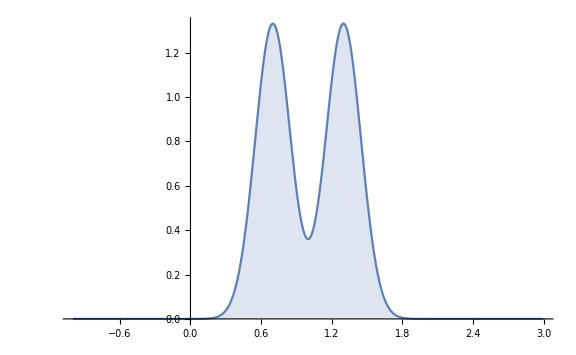

```mathematica
Plot[PDF[distr,x],{x,-1,3},Filling->Axis, ImageSize->Large, PlotRange->All]
```

```mathematica
stateaug0 = Join[state0,Π0];
```

### Equation

```mathematica
n = Length@statelist;
m = Length@Paramslist;
Kr = 3*IdentityMatrix[m];
```

```mathematica
abks[t_?NumericQ, statoaug_?(VectorQ[#,NumericQ]&)]:=Module[{q,ν,νr,s,Mn,Cn,Gn,Mdn,Γn,e,τ,νdot,qdot,statoaugdot, uΠ,stato,Mhat,Chat,Mdhat,Ghat, νrdot},
stato = statoaug[[1;;n]];
q = stato[[1;;7]];
ν = stato[[8;;9]];
νr = νref[t,q];
νrdot = νrefdot[t,stato];
s = νr - ν;
Mn = M[q];
Cn = Cb[stato];
Gn = Gb[q];
Mdn = Mbd[stato];
Γn = Γ[q];
e = ep[t, q];
Mhat = Ma[statoaug];
Chat = Cba[statoaug];
Mdhat = Mbda[statoaug];
Ghat = Gba[statoaug];

τ = Mhat.νrdot + (Chat+Mdhat).νr + Ghat + Kd.s + Γnᵀ.e;
Sow[{t,τ}];
νdot = Inverse[Mn].(τ - (Cn+Mdn).ν - Gn);
qdot = L[q].ν;
 uΠ = Br[stato, νr, νrdot]ᵀ.s;
statoaugdot = Join[qdot,νdot, uΠ]
];
```

### Simulation

```mathematica
{solaugstate,τadapt} = NDSolveValue[{augstate'[t]==abks[t,augstate[t]],augstate[0]== stateaug0},augstate,{t,t0,tfin}]//Reap;
```

```mathematica
{timead,τad}={τadapt[[1,All,1]],τadapt[[1,All,2]]};
```

```mathematica
{τ1ad,τ2ad}=(Interpolation@DeleteDuplicatesBy[{timead,τad[[All,#]]}ᵀ,First])&/@{1,2};
```

```mathematica
Plot[{τ1ad[t],τ2ad[t]},{t,t0,tfin},PlotLegends->{"τR","τL"},AxesLabel->{"t","τ"}, ImageSize->Large]//Rasterize
```

-Graphics-

```mathematica
Plot[Evaluate[{τ1ad[t]-τ1[t],τ2ad[t]-τ2[t]}],{t,t0,tfin},PlotLegends->{"τR","τL"},AxesLabel->{"t","τ"},PlotRange->All, PlotLabel->"τ Difference", ImageSize->Large]//Rasterize
```

-Graphics-

```mathematica
errabks[t_]:=Module[{stato},
stato = solaugstate[t];
q = stato[[1;;7]];
ep[t,q]
];
```

```mathematica
Plot[{errabks[t][[1]],errabks[t][[2]]},{t,t0,tfin},PlotLegends->{"ex","ey"},PlotLabel->"errore di posizione adaptive backstepping",AxesLabel->{"t","err_pos"}, PlotRange->All, ImageSize->Large]//Rasterize
```

-Graphics-

```mathematica
Plot[{errabks[t][[1]],errabks[t][[2]],errbks[t][[1]],errbks[t][[2]]},{t,t0,tfin},PlotLegends->{"ex_adaptive","ey_adaptive","ex","ey"},PlotLabel->"error comparison",AxesLabel->{"t","err_pos"}, ImageSize->Large]//Rasterize
```

-Graphics-

```mathematica
eParams[t_] := Module[{stato},
stato = solaugstate[t];
(Paramslist/.numlaw)-stato[[n+1;;n+m]]
]
```

```mathematica
Plot[{eParams[t][[1]],eParams[t][[2]]},{t,t0,tfin},PlotLegends->{"e_m1","e_m2"},PlotLabel->"errore di stima delle masse m1 e m2 del braccio destro" ,AxesLabel->{"t","err"}, ImageSize->Large]//Rasterize
```

-Graphics-

```mathematica
Plot[{eParams[t][[3]],eParams[t][[4]],eParams[t][[5]],eParams[t][[6]],eParams[t][[7]],eParams[t][[8]]},{t,t0,tfin},PlotLegends->{"e_m3","e_m4","e_m5","e_m6","e_m7","e_m8"},PlotLabel->"errore di stima delle masse dei 2 parallelogrammi connessi al braccio destro" ,AxesLabel->{"t","err"}, ImageSize->Large]//Rasterize
```

-Graphics-

```mathematica
Plot[{eParams[t][[9]],eParams[t][[10]]},{t,t0,tfin},PlotLegends->{"e_ml1","e_ml2"},PlotLabel->"errore di stima delle masse del braccio sinistro" ,AxesLabel->{"t","err"}, ImageSize->Large]//Rasterize
```

-Graphics-

```mathematica
Plot[{eParams[t][[11]],eParams[t][[12]],eParams[t][[13]]},{t,t0,tfin},PlotLegends->{"e_me","e_f", "e_fy"},PlotLabel->"errore di stima dei parametri del coupler" ,AxesLabel->{"t","err"}, ImageSize->Large]//Rasterize
```

-Graphics-

```mathematica
MatrixPlot[Br[statelist, νreflist, νrefdotlist],ColorFunction->"Monochrome",AspectRatio->(1/4),Mesh-> All, ImageSize->Large]//Rasterize
```

-Graphics-

```mathematica
plotqra[t_]:= Module[{stato,q},
stato = solaugstate[t];
q = stato[[1;;2]]
];
```

```mathematica
plotqla[t_]:= Module[{stato,q},
stato = solaugstate[t];
q = stato[[3;;4]]
];
```

```mathematica
plotea[t_]:= Module[{stato,q},
stato = solaugstate[t];
q = stato[[5;;7]]
];
```

```mathematica
Plot[{plotqra[t][[1]],plotqra[t][[2]]},{t,t0,tfin}, PlotLegends->{"qr1","qr2"},AxesLabel->{"t","qRight"}, ImageSize->Large]//Rasterize
```

-Graphics-

```mathematica
Plot[{plotqla[t][[1]],plotqla[t][[2]]},{t,t0,tfin}, PlotLegends->{"ql1","ql2"},AxesLabel->{"t","qLeft"}, ImageSize->Large]//Rasterize
```

-Graphics-

```mathematica
Plot[{plotea[t][[1]],plotea[t][[2]], plotea[t][[3]]},{t,t0,tfin}, PlotLegends->{"xEE","yEE","γ"},AxesLabel-> {"t","qEE"}, ImageSize->Large]//Rasterize
```

-Graphics-

### Movie

```mathematica
man1 = Manipulate[Scene[solaugstate[t]],{t,t0,tfin}];
```

```mathematica
ManToGif[man_, name_String, n_Integer]:=Module[{a},
a = FileNameJoin[{NotebookDirectory[], name<> ".avi"}];
Export[name<> ".gif",Import[ 
Export[a, man]
,"ImageList"][[1;;-1;;n]]]
];
```

```mathematica
Coup[stato_, t_]:= Module[{pos,s},
pos[s_] =Append[Evaluate[Table[Indexed[stato[s], i], {i,5,6}]],0];
ParametricPlot3D[pos[s], {s,t0, t}, PlotStyle->Red]
]
```

```mathematica
ToGif[stato_, step_, name_String] :=Export[
 FileNameJoin[{NotebookDirectory[], name<> ".avi"}],
 Table[
Show[Scene[stato[s]], ref3D[s],Coup[stato, s]], 
	{s,t0+0.001,tfin, step}
]
]
```

```mathematica
ToGif[solaugstate, 0.15, "sim_traj"]
```

/home/francesco/uni/Robotica/Tavole/Delta Robot/mathematica/sim_traj.avi

## Trace Control

## Trace

```mathematica
(*traccia= Block[{xc, yc,xmax,ymax, x, y, center},
center = {0,-0.7};
xc = center[[1]];
yc = center[[2]];
xmax = 0.2;
ymax = 0.1;
f[x_]:= -2Sqrt[-x^2+1]x;
(f[(x-xc)/xmax])^2 - (+y/ymax - yc/ymax)^2 //FullSimplify
];*)
```

```mathematica
traccia= Block[{center,xmax,ymax, x, y,R},
center = {0,-0.7};
xmax = 0.2;
ymax = 0.1;
R = 0.1;
(x-center[[1]])^2 + (y - center[[2]])^2- R^2//FullSimplify
]
```

0.48+x^2+y (1.4+y)

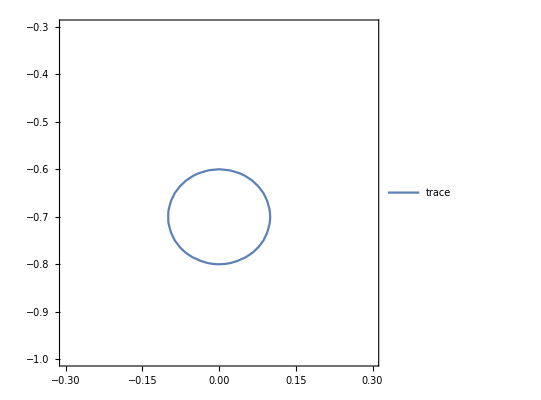

```mathematica
plottrace = ContourPlot[traccia == 0, {x,-0.3,0.3},{y,-0.3,-1}, PlotLegends->{"trace"}]
```

```mathematica
Clear[T,Td, STd]
```

```mathematica
pos = {x,y};
```

```mathematica
T[{x_,y_}] = traccia;
```

```mathematica
Td[{x_,y_}] = {D[T[pos] ,{{x,y}}]}//FullSimplify;
```

```mathematica
Td[pos]//Dimensions
```

{1,2}

```mathematica
STd[{x_,y_}]=(#*Denominator[#[[1,1]]])&@ NullSpace[Td@pos]//FullSimplify//Chop//Transpose
```

{{-0.7-1. y},{1. x}}

```mathematica
STd[{0,-0.7}]//Dimensions
```

{2,1}

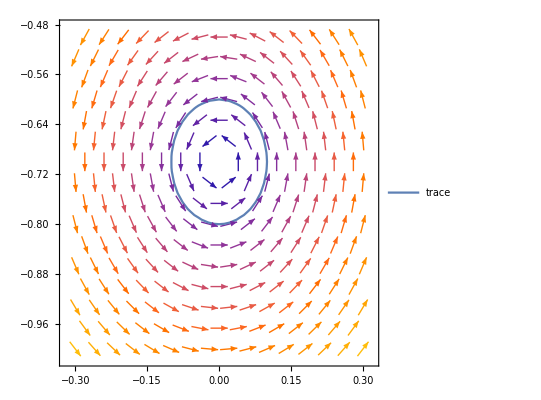

```mathematica
Show[VectorPlot[STd[pos],{x,-0.3,0.3},{y,-0.5,-1}],plottrace]
```

```mathematica
NormS[{x_,y_}] = (Sqrt[#ᵀ.# ]&@STd[pos])[[1,1]]//FullSimplify;
```

```mathematica
NormS[{0,-0.7}]//FullSimplify
```

0.

```mathematica
(Td@pos).STd@pos  //Chop//FullSimplify
```

{{0.}}

```mathematica
First[STd[pos]ᵀ]
```

{-0.7-1. y,1. x}

```mathematica
Q[{x_,y_}] = T[pos]*Td[pos]//FullSimplify;
```

```mathematica
Q[pos].STd[pos]//FullSimplify
```

{{0.}}

## Kinematic Control

```mathematica
vd = 40;
α = 0.1;
```

```mathematica
uref[statepattern] =- Γinv[qlist[[1;;4]]].(Q[{xEE,yEE}]ᵀ*vd - STd[{xEE,yEE}]*α/NormS[{xEE,yEE}])//Simplify;
```

```mathematica
eqctc[t_?NumericQ, stato_?(VectorQ[#,NumericQ]&)]:= Module[{x,v, α, u, q, A, pos, statodot,x0, y, y0},
pos = stato[[5;;6]];
q = stato[[1;;4]];
A = Q[pos]ᵀ;
v = 40;
α = 0.1/NormS[pos];
(*u =- Γinv[q].(A*v - STd[pos]*α);*)
u = uref[Join[stato,{0,0}]];
Sow[{u,t}];
statodot = L[q].u;
First@Transpose@statodot
];
```

```mathematica
eqnstk = {stat'[t] == eqctc[t,stat[t]], stat[t0] == stato0};
```

```mathematica
{soltracekin[s_] , tautrace}= NDSolveValue[eqnstk, stat[s], {t,t0,tfin}]//Reap;
```

```mathematica
{timetrace, τtrace} = {tautrace[[1,All,2]], tautrace[[1,All,1]]};
```

```mathematica
τtrace[[All,1,1]]//Dimensions
```

{371}

```mathematica
timetrace//Dimensions
```

{371}

```mathematica
{u1, u2}=Interpolation@DeleteDuplicatesBy[{timetrace, τtrace[[All,#,1]]}ᵀ, First]&/@{1,2}
```

{InterpolatingFunction[…],InterpolatingFunction[…]}

```mathematica
Plot[{u1[t],u2[t]},{t,t0,tfin}];
```

```mathematica
Manipulate[Scene[soltracekin[t]],{t,t0,tfin}];
```

```mathematica
plotpos = ParametricPlot[Evaluate@Table[Indexed[soltracekin[t],i],{i,5,6}],{t,t0,tfin}, PlotStyle->Directive[Red, Dashed], PlotLegends->{"simulation"}, PlotRange->{{-0.3,0.3},{-0.5,-1}}];
```

```mathematica
Show[plotpos,plottrace]//Rasterize
```

-Graphics-

## Backstepping Control

### parameters

```mathematica
urefdot[statepattern]=Module[{a,b,c},
a = D[uref[state[t]],t]//Simplify;
b = a/.Thread[q[t]->qlist];
c = b/.Thread[q'[t]-> L[qlist].νlist];
c//Simplify
];
```

### equation

```mathematica
bkstrace[t_?NumericQ, stato_?(VectorQ[#,NumericQ]&)]:=Module[{q,ν,νr,s,Mn,Cn,Gn,Mdn,Γn,e,τ,νdot,qdot,statodot,pos, νrdot},
q = stato[[1;;7]];
pos = q[[5;;6]];
ν = stato[[8;;9]];
νr = uref[stato];
νrdot = urefdot[stato];
s = νr - ν;
Mn = M[q];
Cn = Cb[stato];
Gn = Gb[q];
Mdn = Mbd[stato];
Γn = Γ[q];

τ =Flatten[ Mn.νrdot + (Cn+Mdn).νr + Gn + Kd.s - Γnᵀ.Q[pos]ᵀ];
Sow[{t,τ}];
νdot = Inverse[Mn].(τ - (Cn+Mdn).ν - Gn);
qdot = L[q].ν;
statodot = Join[qdot,νdot]
];
```

```mathematica
bkstrace[0,state0]
```

{3.32493,-1.58264,-3.30868,2.79965,0.6,0.8,0.,-33.8997,23.8748}

```mathematica
eqnsbkstrace = {stat'[t] == bkstrace[t,stat[t]], stat[0] == state0};
```

### Simulation

```mathematica
{solstate,τsol} = NDSolveValue[eqnsbkstrace,stat,{t,t0,tfin}]//Reap;
```

```mathematica
{time, τsim}=Module[{tempo,tau},
tempo = First[τsol][[All,1]];
tau = First[τsol][[All,2]];
{tempo,tau}
];
```

```mathematica
{τ1,τ2}=(Interpolation@DeleteDuplicatesBy[{time,τsim[[All,#]]}ᵀ,First])&/@{1,2};
```

```mathematica
Plot[{τ1[t],τ2[t]},{t,t0,tfin},PlotLegends->{"τR","τL"},AxesLabel->{"t","τ"}, ImageSize->Large]//Rasterize
```

-Graphics-

### movie

```mathematica
plotpos = ParametricPlot[Evaluate@Table[Indexed[solstate[t],i],{i,5,6}],{t,t0,tfin}, PlotStyle->Directive[Red, Dashed], PlotLegends->{"simulation"}, PlotRange->{{-0.3,0.3},{-0.5,-1}}];
```

```mathematica
Show[plotpos,plottrace, ImageSize-> Large]//Rasterize
```

-Graphics-

```mathematica
Manipulate[Scene[solstate[t]],{t,t0,tfin}]
```

## Adaptive Backstepping Control

### equation

```mathematica
abkstrace[t_?NumericQ, statoaug_?(VectorQ[#,NumericQ]&)]:=Module[{q,ν,νr,s,Mn,Cn,Gn,Mdn,Γn,e,τ,νdot,qdot,statoaugdot, uΠ,stato,Mhat,Chat,Mdhat,Ghat, νrdot,pos},
stato = statoaug[[1;;n]];
q = stato[[1;;7]];
ν = stato[[8;;9]];
pos = q[[5;;6]];
νr = uref[stato]//Flatten;
νrdot = urefdot[stato]//Flatten;
s = νr - ν;
Mn = M[q];
Cn = Cb[stato];
Gn = Gb[q];
Mdn = Mbd[stato];
Γn = Γ[q];
e = ep[t, q];
Mhat = Ma[statoaug];
Chat = Cba[statoaug];
Mdhat = Mbda[statoaug];
Ghat = Gba[statoaug];

τ = Mhat.νrdot + (Chat+Mdhat).νr + Ghat + Kd.s + Γnᵀ.Flatten[Q[pos]ᵀ];
Sow[{t,τ}];
νdot = Inverse[Mn].(τ - (Cn+Mdn).ν - Gn);
qdot = L[q].ν;
 uΠ = Br[stato, νr, νrdot]ᵀ.s;
statoaugdot = Join[qdot,νdot, uΠ]
];
```

```mathematica
abkstrace[0,stateaug0]
```

{3.32493,-1.58264,-3.30868,2.79965,0.6,0.8,0.,-36.7882,27.0552,-2.02706,-3.53334,0.,-2.02706,-4.05412,-4.05412,-3.53318,-3.13204,-0.303389,-1.97443,-3.136,0.,0.}

```mathematica
eqnsabkstrace = {stat'[t] == abkstrace[t,stat[t]], stat[0] == stateaug0};
```

### Simulation

```mathematica
{solstate,τsol} = NDSolveValue[eqnsabkstrace,stat,{t,t0,tfin}]//Reap;
```

```mathematica
{timead,τad}={τsol[[1,All,1]],τsol[[1,All,2]]};
```

```mathematica
{τ1ad,τ2ad}=(Interpolation@DeleteDuplicatesBy[{timead,τad[[All,#]]}ᵀ,First])&/@{1,2};
```

```mathematica
Plot[{τ1ad[t],τ2ad[t]},{t,t0,tfin},PlotLegends->{"τR","τL"},AxesLabel->{"t","τ"}, ImageSize->Large]//Rasterize
```

-Graphics-

```mathematica
eParams[t_] := Module[{stato},
stato = solstate[t];
(Paramslist/.numlaw)-stato[[n+1;;n+m]]
]
```

```mathematica
Plot[{eParams[t][[1]],eParams[t][[2]]},{t,t0,tfin},PlotLegends->{"e_m1","e_m2"},PlotLabel->"errore di stima delle masse m1 e m2 del braccio destro" ,AxesLabel->{"t","err"}, ImageSize->Large]//Rasterize
```

-Graphics-

```mathematica
Plot[{eParams[t][[3]],eParams[t][[4]],eParams[t][[5]],eParams[t][[6]],eParams[t][[7]],eParams[t][[8]]},{t,t0,tfin},PlotLegends->{"e_m3","e_m4","e_m5","e_m6","e_m7","e_m8"},PlotLabel->"errore di stima delle masse dei 2 parallelogrammi connessi al braccio destro" ,AxesLabel->{"t","err"}, ImageSize->Large]//Rasterize
```

-Graphics-

```mathematica
Plot[{eParams[t][[9]],eParams[t][[10]]},{t,t0,tfin},PlotLegends->{"e_ml1","e_ml2"},PlotLabel->"errore di stima delle masse del braccio sinistro" ,AxesLabel->{"t","err"}, ImageSize->Large]//Rasterize
```

-Graphics-

```mathematica
Plot[{eParams[t][[11]],eParams[t][[12]],eParams[t][[13]]},{t,t0,tfin},PlotLegends->{"e_me","e_f", "e_fy"},PlotLabel->"errore di stima dei parametri del coupler" ,AxesLabel->{"t","err"}, ImageSize->Large]//Rasterize
```

-Graphics-

### movie

```mathematica
reftrace = ParametricPlot3D[0.1{Cos[t],Sin[t]-7,0},{t,0,2Pi},PlotStyle->Blue];
```

```mathematica
Show[Scene@state0,ParametricPlot3D[0.1{Cos[t],Sin[t]-7,0},{t,0,2Pi},PlotStyle->Purple, PlotLegends->{"trace"}] ]//Rasterize;
```

-Graphics-

```mathematica
plotpos = ParametricPlot[Evaluate@Table[Indexed[solstate[t],i],{i,5,6}],{t,t0,tfin}, PlotStyle->Directive[Red, Dashed], PlotLegends->{"simulation"}, PlotRange->{{-0.3,0.3},{-0.5,-1}}];
```

```mathematica
Show[plotpos,plottrace]//Rasterize;
```

```mathematica
Manipulate[Scene[solstate[t]],{t,t0,tfin}];
```

```mathematica
ToGiftrace[stato_, step_, name_String] :=Export[
 FileNameJoin[{NotebookDirectory[], name<> ".avi"}],
 Table[
Show[Scene[stato[s]], reftrace,Coup[stato, s]], 
	{s,t0+0.001,tfin, step}
]
]
```

```mathematica
(*ToGiftrace[solstate, 0.15, "sim_trace"]
```

/home/francesco/uni/Robotica/Tavole/Delta Robot/mathematica/sim_trace.avi

## Computed Torque

### equation

```mathematica
state0 = Join[stato0, {0,0}];
```

```mathematica
ctorque[t_?NumericQ, stato_?(VectorQ[#,NumericQ]&)]:=Module[{q,ν,νr,Mn,Cn,Gn,Mdn,Γn,e,τ,νdot,qdot,statodot,pos,Dn, h, ep, ev},
q = stato[[1;;7]];
pos = q[[5;;6]];
ν = stato[[8;;9]];
Mn = M[q];
Dn = Db[stato];
Mdn = Mbd[stato];
Γn = Γ[q];
Gn = Gb[q];
ep = trajdes[t]-pos;
qdot = L[q].ν;
ev = veldes[t] - Γn.ν;

h= Dn.ν + Gn - Mn.Γinv[stato].Γdot[stato].ν ;
τ = h +  Mn.Γinv[stato].(accdes[t] + 4ev+4ep);
Sow[{t,τ}];
νdot = Inverse[Mn].(τ - (Dn).ν - Gn);
statodot = Join[qdot,νdot]
];
```

```mathematica
eqnsctorque= {stat'[t] == ctorque[t,stat[t]], stat[0] == state0};
```

### Simulation

```mathematica
{solstate,τsol} = NDSolveValue[eqnsctorque,stat,{t,t0,tfin}]//Reap;
```

```mathematica
{time, τsim}=Module[{tempo,tau},
tempo = First[τsol][[All,1]];
tau = First[τsol][[All,2]];
{tempo,tau}
];
```

```mathematica
{τ1,τ2}=(Interpolation@DeleteDuplicatesBy[{time,τsim[[All,#]]}ᵀ,First])&/@{1,2};
```

```mathematica
Plot[{τ1[t],τ2[t]},{t,t0,tfin},PlotLegends->{"τR","τL"},AxesLabel->{"t","τ"}, ImageSize->Large]//Rasterize
```

-Graphics-

```mathematica
errctorque[t_]:=Module[{stato,q},
stato = solstate[t];
q = stato[[1;;7]];
ep[t,q]
];
```

```mathematica
Plot[{errctorque[t][[1]],errctorque[t][[2]]},{t,t0,tfin},PlotLegends->{"ex","ey"},PlotLabel->"errore di posizione computerd torque",AxesLabel->{"t","err_pos"}, PlotRange->All, ImageSize->Large]//Rasterize
```

-Graphics-

### movie

```mathematica
plotpos = ParametricPlot[Evaluate@Table[Indexed[solstate[t],i],{i,5,6}],{t,t0,tfin}, PlotStyle->Directive[Red, Dashed], PlotLegends->{"simulation"}, PlotRange->{{-0.3,0.3},{-0.5,-1}}];
```

```mathematica
Show[plotpos, ImageSize-> Large]//Rasterize
```

-Graphics-

```mathematica
Manipulate[Scene[solstate[t]],{t,t0,tfin}]
```